```mathematica
SetDirectory[NotebookDirectory[]];
```

# T_scaling

## data

```mathematica
fpi=Flatten[Import["../mub0/buffer/fpi.dat"]];
T0=Flatten[Import["../mub0/buffer/TMeV.dat"]];
t=(T0-T0[[1]])/T0[[1]];
datamub0=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
datamub0linear=Transpose[{-t[[2;;Length[t]]],fpi[[2;;Length[t]]]}];
b1mub0=Transpose[{-t[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub0[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T0]-2}]]}];

fpi=Flatten[Import["../mub550/buffer/fpi.dat"]];
T0=Flatten[Import["../mub550/buffer/TMeV.dat"]];
t=(T0-T0[[1]])/T0[[1]];
datamub550=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
datamub550linear=Transpose[{-t[[2;;Length[t]]],fpi[[2;;Length[t]]]}];
b1mub550=Transpose[{-t[[2;;Length[t]-2]],Flatten[Table[FindFit[datamub0[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T0]-2}]]}];
```

## Fit

```mathematica
(*A=Exp[1.532];*)
δ=5.0;
delta=5.0;
beta=0.4;
nu=0.804;
A1=4.7;
cm1=-0.2;
omega=0.7459;
θt=nu*omega;
fitfun=A x^β(1+cm x^θt1);
fitfun2=A+β x(*+Log[(1+cm Exp[x]^θt)]*);
fitfun3=A1+beta x+Log[(1+cm Exp[x]^θt)];
fitfun4=A+β x+Log[(1+cm Exp[x]^θt)];
```

```mathematica
fitbetaLO=Transpose[{-t[[2;;Length[t]-2]],Flatten[Table[NonlinearModelFit[datamub0[[i-1;;i+1]],fitfun2,{A,β},x][[1]][[2]][[2]][[2]],{i,2,Length[t]-2}]]}];
```

```mathematica
fitbeta=Transpose[{-t[[2;;Length[t]-2]],Flatten[Table[NonlinearModelFit[datamub0[[i-1;;i+1]],fitfun4,{A,β,cm},x][[1]][[2]][[2]][[2]],{i,2,Length[t]-2}]]}];
```

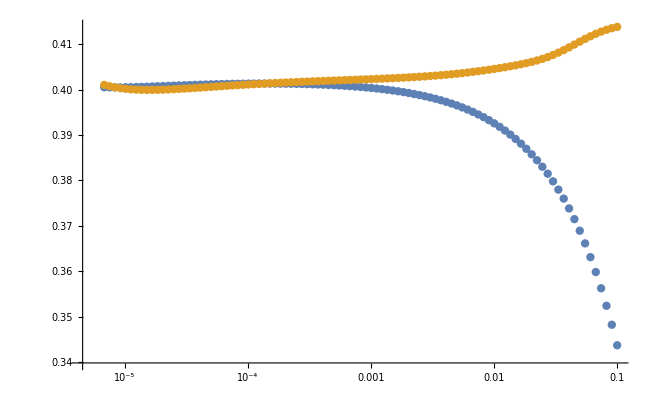

```mathematica
Show[ListPlot[{b1mub0,fitbeta},ScalingFunctions->{"Log"},PlotRange->{All,All}]]
```

```mathematica
Export["./NLObeta.dat",fitbeta]
```

./NLObeta.dat

## Fit mub

```mathematica
(*A=Exp[1.532];*)
δ=5.0;
delta=5.0;
beta=0.4;
nu=0.804;
A1=4.7;
cm1=-0.2;
omega=0.7459;
θt=nu*omega;
fitfun=A x^β(1+cm x^θt1);
fitfun2=A+β x(*+Log[(1+cm Exp[x]^θt)]*);
fitfun3=A1+beta x+Log[(1+cm Exp[x]^θt)];
fitfun4=A+β x+Log[(1+cm Exp[x]^θt)];
```

```mathematica
fitbetamub550=Transpose[{-t[[2;;Length[t]-2]],Flatten[Table[NonlinearModelFit[datamub550[[i-1;;i+1]],fitfun4,{A,β,cm},x][[1]][[2]][[2]][[2]],{i,2,Length[t]-2}]]}];
```

NonlinearModelFit::nrlnum: 在 {A,β,cm} = {6.00901,0.634128,-3.59347} 处，函数值 {-1.65099+0. ⅈ,-2.50122+0. ⅈ,-3.14947+3.14159 ⅈ} 不是由实数组成的维度为 {3} 的列表.

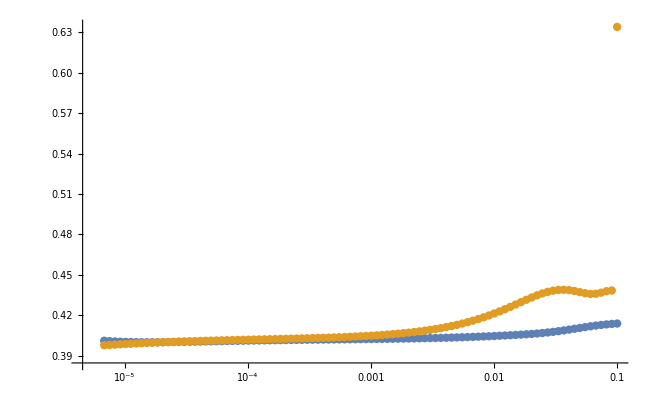

```mathematica
Show[ListPlot[{fitbeta,fitbetamub550},ScalingFunctions->{"Log"},PlotRange->{All,All}]]
```

```mathematica
Export["./NLObetamub550.dat",fitbetamub550]
```

./NLObetamub550.dat